```mathematica
zres = 1/(1/r+I*ω c-I/(ω l));
zresg = -I*zr*Cot[ω/ω0*π];
zin = -I/(ω cin);
```

```mathematica
ztotg=zresg+zin;
ztot=zres+zin;
```

```mathematica
s11 = FullSimplify[(ztot-z0)/(ztot+z0)];
s11g = FullSimplify[(ztotg-z0)/(ztotg+z0)];
```

```mathematica
wp = {c->π/2,l->2/π,r->10000000000,cin->0.1,z0->1,zr->1,ω0->1}
```

{c→π/2,l→2/π,r→10000000000,cin→0.1,z0→1,zr→1,ω0→1}

```mathematica
Abs[zresg] /.wp /.{ω->1.2}
```

1.37638

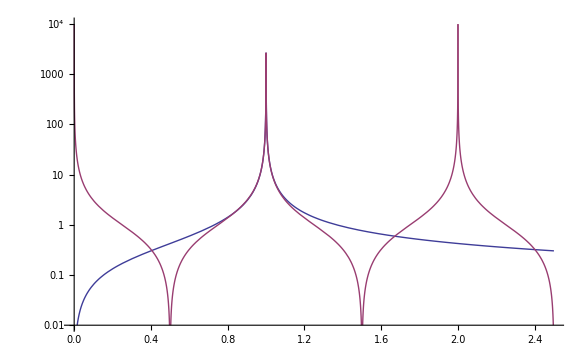

```mathematica
LogPlot[{Abs[zres]/. wp,Abs[zresg]/. wp} ,{ω,0.,2.5},PlotRange->{0.01,1*^4}]
```

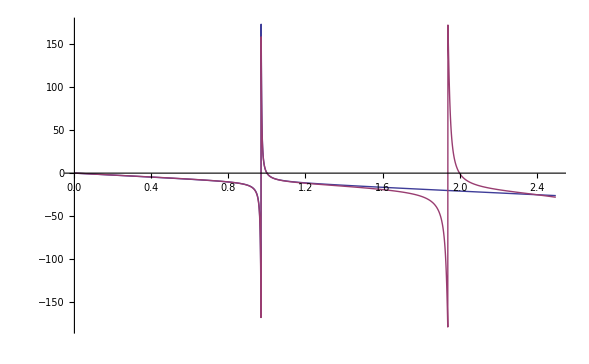

```mathematica
Plot[{Arg[s11]*180/π/. wp,Arg[s11g]*180/π/. wp} ,{ω,0.,2.5},PlotRange->Full]
```